```mathematica
Remove["Global`*"]
```

```mathematica
Get["IB\\IonDispCurves.wl"]
```

```mathematica
Needs["HotDisp`","IB\\HotDisp.wl"]
Needs["IonDispCurves`","IB\\IonDispCurves.wl"]
Needs["CutOffs`"]
uhEigenMods=Flatten@Import["UHwaves\\EigenFreq.txt","Data"];
```

```mathematica
ωn=uhEigenMods[[28]]2 π 10^9;
ωm=uhEigenMods[[18]]2 π 10^9;
ωI=ωm-ωn;
xl=leftCutOff[ωm];
xr=rightCutOff[ωm];
xr2=x/.FindRoot[Abs[(Derivative[0,1][qminus][ωm,x])/(Re@qminus[ωm,x])^2]-1/3,{x,xl 0.4+xr 0.6,(xl+xr)/2,xr}];
xl2=x/.FindRoot[Abs[(Derivative[0,1][qminus][ωm,x])/(Re@qminus[ωm,x])^2]-1/3,{x,xl 0.6+xr 0.4,xl,(xl+xr)/2}];
```

```mathematica
IDC=IonDispCurves[ωI,xl2,xr2];
rngL=Table[IF⟦1,1⟧,{IF,IDC[[2]]}];
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(*rngL=Table[IF⟦1,1⟧,{IF,IDC[[2]]}];
rngL2=Table[{IDC[[Ii,ri,3,1,3]],IDC[[Ii,ri,3,1,-3]]},
{ri,4},{Ii,1,2}
];*)
```

```mathematica
(*SafeFindRoot[f_,x1_,x2_]:=Module[{sol,α=0.9},sol=x/.FindRoot[f[x],{x,x1(1-α)+α x2,x1,x2}];If[Abs[f[sol]]<0.001,{x1,sol},{},{}]]
rngL2=Table[SafeFindRoot[Abs[(Derivative[2][IDC[[Ii,ri]]][#])/(IDC[[Ii,ri]][#])^2]-0.005&,rngL[[ri,1]],rngL[[ri,2]]],{ri,3},{Ii,2}];
AppendTo[rngL2,{rngL[[4]],rngL[[4]]}];*)
```

```mathematica
qL={qplus,qminus};
repL=Table[{qm->qm2,qn->qn2},{qn2,qL},{qm2,qL}];
qmqn=Flatten[(qm[ωm,#]+qn[ωn,#])&/.repL];

repL2=Map[Flatten[#,1]&,
Table[{ri->ri2,qI->qI2,qm->qm2,qn->qn2},{ri2,Length@rngL},{qI2,IDC},{qn2,qL},{qm2,qL}]
,{2}];

preExp=Abs[DIBq[qI[[ri]][#],ωm-ωn,#]Derivative[1,0,0][Duh][qn[ωn,#],ωn,#]Derivative[1,0,0][Duh][qm[ωm,#],ωm,#]]^(-1/2)&/.repL2;
χI=(-el/me ωpe[#]^2 ωm/(ωm^2-ωce[#]^2)ωn/(ωn^2-ωce[#]^2)ωI/(ωI^2-ωce[#]^2)qm[ωm,#] qn[ωn,#] qI[[ri]][#]((qI[[ri]][#])/ωI+qm[ωm,#]/ωm-qn[ωn,#]/ωn))&/.repL2;
χn=(-el/me ωpe[#]^2 ωm/(ωm^2-ωce[#]^2)ωn/(ωn^2-ωce[#]^2)ωI/(ωI^2-ωce[#]^2)qm[ωm,#] qn[ωn,#] qI[[ri]][#](qn[ωn,#]/ωn+qm[ωm,#]/ωm-(qI[[ri]][#])/ωI))&/.repL2;
```

```mathematica
preExp=Abs[DIBqPW[qI[[ri]][#],ωm-ωn,#]Derivative[1,0,0][Duh][qn[ωn,#],ωn,#]Derivative[1,0,0][Duh][qm[ωm,#],ωm,#]]^(-1/2)&/.repL2;
```

```mathematica
(*With[{nSteps=100},
Appr[f_]:=Table[
Interpolation[Table[With[{x=rngL2[[ri,Ii,1]]+(rngL2[[ri,Ii,2]]-rngL2[[ri,Ii,1]])Log[nSteps,n]^2},{x,f[[ri,Ii,uhi]][x]}],{n,nSteps}]],
{ri,Length@rngL2},{Ii,2},{uhi,4}];
(*rngL2=Table[{rngL[[ri,1]],rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[nSteps,nSteps-1]^2},{ri,Length@rngL}];*)
]*)
With[{nSteps=100},
Appr[f_]:=Table[
Interpolation[Table[With[{x=rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[nSteps,n]},{x,f[[ri,Ii,uhi]][x]}],{n,nSteps}]],
{ri,Length@rngL},{Ii,2},{uhi,4}];
(*rngL2=Table[{rngL[[ri,1]],rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[nSteps,nSteps-1]^2},{ri,Length@rngL}];*)
]
```

```mathematica
{χIAppr,χnAppr,preExpAppr}=Appr/@{χI,χn,preExp};
```

General::munfl: 1/((5.70846×10^9)^39) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((5.70846×10^9)^38) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((5.70846×10^9)^37) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
θ0L=Flatten@Table[π/4((-1)^mi+(-1)^ni),{ni,2},{mi,2}];θL=Table[NDSolveValue[{θ'[x]==IDC[[Ii,ri]][x]-qmqn[[uhi]][x],θ[rngL[[ri,1]]]==θ0L[[uhi]]},θ,{x,rngL[[ri,1]],rngL[[ri,2]]}],{ri,Length[rngL]},{Ii,2},{uhi,4}];
```

### Графики подыинтегральных функций

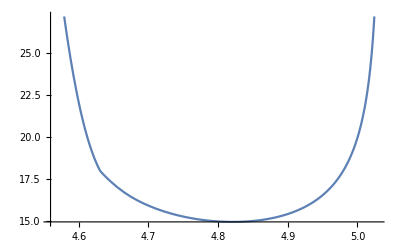
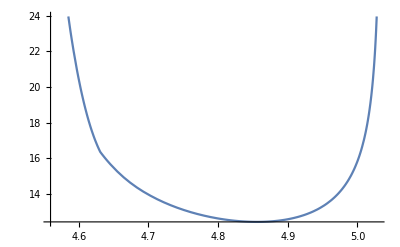
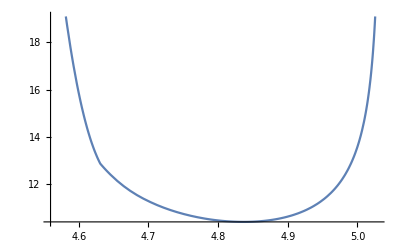
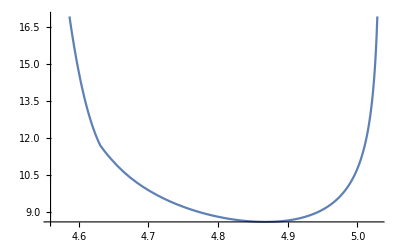
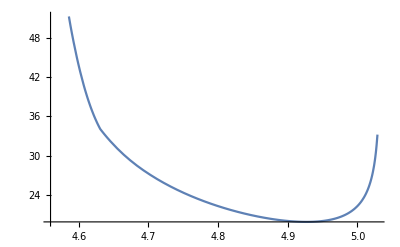
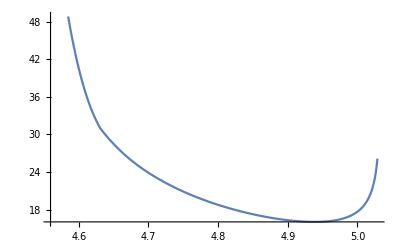
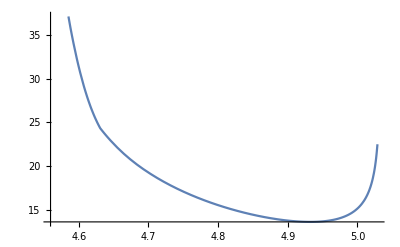
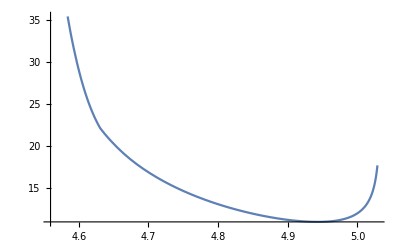

```mathematica
rngL2=Table[{rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[50,1],rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[50,50-1]},{ri,Length@rngL}];
Table[Plot[Re[χIAppr[[ri,Ii,uhi]][ξ]preExpAppr[[ri,Ii,uhi]][ξ]],{ξ,rngL2[[ri,1]],rngL2[[ri,2]]}],{ri,Length@rngL2},{Ii,2},{uhi,4}]
```

### 50 шагов (сошедшийся)

```mathematica
rngL2=Table[{rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[50,1],rngL[[ri,1]]+(rngL[[ri,2]]-rngL[[ri,1]])Log[50,50-1]},{ri,Length@rngL}];
```

```mathematica
DistributeDefinitions[θL,preExpAppr,χIAppr,χnAppr,rngL2];IntL=ParallelTable[NIntegrate[χnAppr[[ri,Ii,uhi]][x]preExpAppr[[ri,Ii,uhi]][x]χIAppr[[ri,Ii,uhi]][ξ]preExpAppr[[ri,Ii,uhi]][ξ] ⅇ^(-ⅈ θL[[ri,Ii,uhi]][x])ⅇ^(ⅈ θL[[ri,Ii,uhi]][ξ]),{x,rngL2[[ri,1]],rngL2[[ri,2]]},{ξ,rngL2[[ri,1]],x},Method->"LocalAdaptive",PrecisionGoal->4],{ri,Length@rngL2-1},{Ii,2},{uhi,4}]
Total[IntL[[;;3]],3]
AbsArg@%
```

{{{-1.14775-4.68996 ⅈ,-0.274949-4.9319 ⅈ,-0.584255-7.22893 ⅈ,-12.1275-0.44611 ⅈ},{-23.7186-13.5178 ⅈ,-47.5261-5.07058 ⅈ,-1.70569+9.43416 ⅈ,-1.69847+6.98668 ⅈ}},{{-0.072875-1.48813 ⅈ,-0.0708279-1.22261 ⅈ,-0.0910305-1.42745 ⅈ,-0.679629+1.9604 ⅈ},{-17.3387+228.117 ⅈ,-52.1839+52.9578 ⅈ,-19.6205+72.892 ⅈ,-2.60775+48.4202 ⅈ}},{{-0.160093-2.08412 ⅈ,-0.283456-1.89794 ⅈ,-0.412682-2.27979 ⅈ,-0.116672+1.28106 ⅈ},{4.75619+93.7316 ⅈ,-8.19672+12.9192 ⅈ,8.5567+23.5825 ⅈ,-1.18965+14.6306 ⅈ}}}

```mathematica
AbsCoefTable@IntL
```

1 |  | q_I^- | q_I^+
q_m^++q_n^+ | 4.82836 | 27.3003
q_m^-+q_n^+ | 4.93956 | 47.7958
q_m^++q_n^- | 7.2525 | 9.58712
q_m^-+q_n^- | 12.1357 | 7.19017
2 |  | q_I^- | q_I^+
q_m^++q_n^+ | 1.48991 | 228.775
q_m^-+q_n^+ | 1.22466 | 74.3485
q_m^++q_n^- | 1.43035 | 75.4865
q_m^-+q_n^- | 2.07486 | 48.4904
3 |  | q_I^- | q_I^+
q_m^++q_n^+ | 2.09026 | 93.8522
q_m^-+q_n^+ | 1.91899 | 15.3001
q_m^++q_n^- | 2.31684 | 25.0869
q_m^-+q_n^- | 1.28636 | 14.6789

```mathematica
Total[IntL[[;;3]],3]
AbsArg@%
```

-178.495+520.628 ⅈ

{550.376,1.90108}